```mathematica
ClearAll[σ];
σ[x_] := 1/(1 + Exp[-x]);
```

```mathematica
ClearAll[f];
f[λ_] := NSolve[σ[λ x] == x, x, Reals][[1, 1, 2]];
```

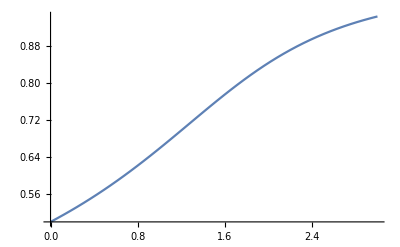

```mathematica
Plot[f[λ], {λ, 0, 3}]
```

Compute f[λ] numerically using an ODE:

```mathematica
With[{func = NDSolve[{ϕ'[x] == (ϕ[x]^2(1 - ϕ[x]))/(1 - x ϕ[x](1 - ϕ[x])), ϕ[0] == 1/2}, ϕ, {x, 0, 3}][[1, 1, 2]]}, Plot[func[x], {x, 0, 3}]]
```

-Graphics-

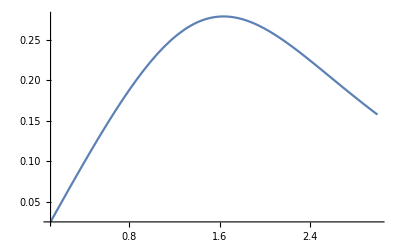

```mathematica
Block[{g},
	g[λ_] := With[{F = f[λ]}, λ F (1 - F)];
	
	Plot[g[λ], {λ, 0.1, 3}]
]
```

```mathematica
With[{λ =1.64}, (λ f[λ](1 - 2f[λ]))/(1 - λ f[λ](1 - f[λ]))]
```

-1.00832

```mathematica
ClearAll[b];
b[λ_] := NSolve[σ[λ/2 + b] == 1/2, b, Reals][[1, 1, 2]];
```

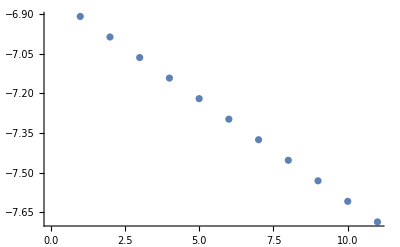

```mathematica
With[{λ = 3.7}, ListPlot[Log[NestList[σ[λ (#-1/2)]&, 1/2 + 0.001, 10] - 1/2]]]
```